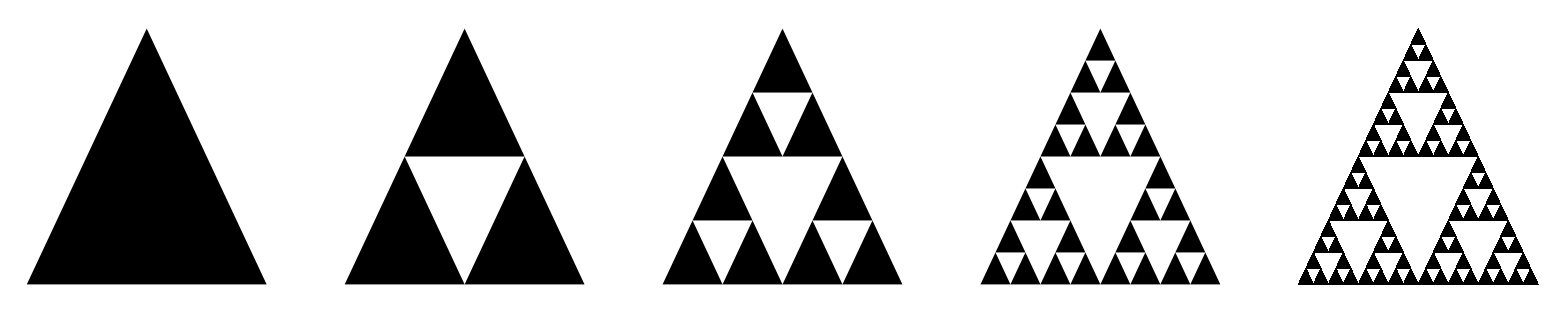

```mathematica
(* Raquel Lippincott - 2017
	Mathematica Notebook *)

Sierpinski[a_, b_,c_, currIt_,exitIt_] := 
	If [currIt < exitIt, {
	Module[{ab, bc, ca, s1, s2, s3,s4},
	ab = (a+b)/2;
	bc = (b+c)/2;
	ca = (c + a)/2;
	s1 = Sierpinski[a, ca, ab, currIt+1, exitIt];
	s2 = Sierpinski[ab, b, bc, currIt+1, exitIt];
	s3 = Sierpinski[bc, c, ca, currIt+1, exitIt];
	{s1, s2, s3}]
	},{
	{a,b,c}
	}]

SierpinskiGasket[iterations_] := Polygon[Partition[Partition[Flatten[Sierpinski[{0,0},{1,2},{2,0},1,iterations]],2],3]]

SierpinskiGasketPlot[iterations_] := 
GraphicsGrid[{Table[Graphics[SierpinskiGasket[i]],{i,1,iterations}]}, ImageSize->Full]


SierpinskiGasketPlot[5]
```